Euler’s Method

```mathematica
Clear["Global`*"]
```

```mathematica
euler[ti_, tf_, xi_, func_, nMax_] := Module[{h, datalist, prev}, h = (tf - ti)/nMax//N;
For[datalist={{ti,xi}};, 
Length[datalist]<= nMax,
AppendTo[datalist, prev + {h, h f@@prev}], 
prev= Last[datalist]];

Return[datalist];
]
```

```mathematica
error[dataset_, func_] := Module[{tlist, xlist, Fxlist}, tlist = dataset[[;;, 1]];
xlist = dataset[[;;, 2]];
Fxlist=func/@tlist;
Return[xlist-Fxlist//Abs//Mean];
]
```

```mathematica
f[t_, x_]= -x t
```

-t x

```mathematica
ff[t_]= ⅇ^(-t^2/2)
```

ⅇ^(-t^2/2)

```mathematica
Table[{(5.0/10^n), error[euler[0,5,1,f,10^n], ff]/(5.0/10^n)}, {n,1,4}]//N
```

{{0.5,0.0746396},{0.05,0.0639748},{0.005,0.0631697},{0.0005,0.0630899}}

__________________________________________________________________

RK4 Method

```mathematica
Clear["Global`*"]
```

```mathematica
rk4[F_,Xθ_,tf_,nmax_]:=Module[{h,datalist,prev,rate1,rate2,rate3,rate4,next},h=(tf-Xθ[[1]])/nmax//N;
For[datalist={Xθ},Length[datalist]<=nmax,AppendTo[datalist,next],prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+h/2 rate1);
rate3=F@(prev+h/2 rate2);
rate4=F@(prev+h rate3);
next=prev+h/6 (rate1+2 rate2+2 rate3+rate4);];
Return[datalist];]
ratefunc[{t_,x_}]={1, -x t};
initial={0, 1};
```

```mathematica
err[dataset_, func_] := Module[{tlist, xlist, Fxlist}, 
tlist = dataset[[;;, 1]];
xlist = dataset[[;;, 2]];
Fxlist = func/@tlist;
Return[xlist-Fxlist//Abs//Mean];
]
```

```mathematica
Solx[t_]= ⅇ^(-t^2/2)
```

ⅇ^(-t^2/2)

```mathematica
ⅇ^(-t^2/2)
```

ⅇ^(-t^2/2)

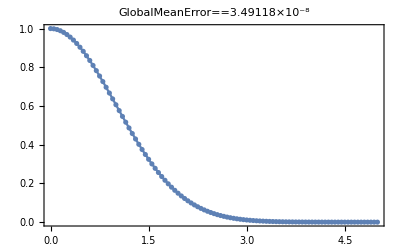

```mathematica
datap= rk4[ratefunc, initial, 5, 100];
Show[ListPlot[datap, PlotRange->Full], Plot[Solx[t], {t, 0,5}], PlotLabel->"GlobalMeanError" == ScientificForm[err[datap, Solx]], Frame->True, PlotStyle->Red]
```

RK2

```mathematica
Clear["Global`*"]
```

```mathematica
rk2[F_,X0_,tf_,nMax_]:=
Module[{h,datalist,prev,rate,rate1, next},
h=(tf-X0[[1]])/nMax//N;
For[datalist={X0},
 Length[datalist]<=nMax,
 AppendTo[datalist,next],
 prev=Last[datalist];
rate=F@prev;
rate1 = F@(prev+ h rate);
next=prev+h/2(rate+ rate1);
];
Return[datalist];
]
ratefunc[{t_,x_}]={1, -x t};
initial={0, 1};
```

```mathematica
err[dataset_, func_] := Module[{tlist, xlist, Fxlist}, 
tlist = dataset[[;;, 1]];
xlist = dataset[[;;, 2]];
Fxlist = func/@tlist;
Return[xlist-Fxlist//Abs//Mean];
]
```

```mathematica
Solx[t_]= ⅇ^(-t^2/2)
```

ⅇ^(-t^2/2)

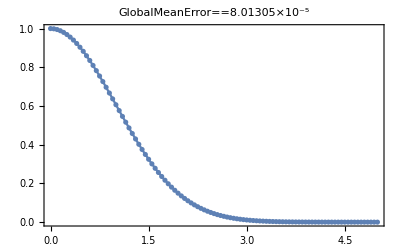

```mathematica
datap= rk2[ratefunc, initial, 5, 100];
Show[ListPlot[datap, PlotRange->Full], Plot[Solx[t], {t, 0,5}], PlotLabel->"GlobalMeanError" == ScientificForm[err[datap, Solx]], Frame->True, PlotStyle->Red]
```